```mathematica
hexToRGB=RGBColor@@(IntegerDigits[ToExpression@StringReplace[#,"#"->"16^^"],256,3]/255.)&;
{COLS,SEL}={{hexToRGB["#ee4266"],hexToRGB["#6ba5ff"]},False}
```

{{RGBColor[0.9333333333333333, 0.2588235294117647, 0.4],RGBColor[0.4196078431372549, 0.6470588235294118, 1.]},False}

## Data Analysis

```mathematica
RELSTART=20;
(*--------------------------------------------*)
If[
SEL,
ID="YorkeysKnob";
PATH ="/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_1_10/ANALYZED/";
confidence=Import["/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/CI.csv"][[2;;All]][[All,3;;All]];
dataRaw={
{{04,01,2011},0.00},{{19,01,2011},0.24},{{01,02,2011},0.70},{{09,02,2011},0.62},{{16,02,2011},0.38},
{{02,03,2011},0.88},{{16,03,2011},0.76},{{30,03,2011},0.98},{{13,04,2011},1.00},{{27,04,2011},0.95}
};
,
ID="Gordonvale";
PATH="/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/GV/Wolbachia_1_10/ANALYZED/";
confidence=Import["/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/GV/CI.csv"][[2;;All]][[All,3;;All]];
dataRaw={
{{04,01,2011},0.00},{{24,01,2011},0.17},{{07,02,2011},0.44},{{21,02,2011},0.49},{{07,03,2011},0.66},
{{21,03,2011},0.68},{{04,04,2011},.79},{{18,04,2011},0.90},{{02,05,2011},.81}
};
];
files=FileNames["E_04_05_0010_0300*.csv",PATH];
files
```

{/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/GV/Wolbachia_1_10/ANALYZED/E_04_05_0010_0300.csv}

{0.57979,0.79196}

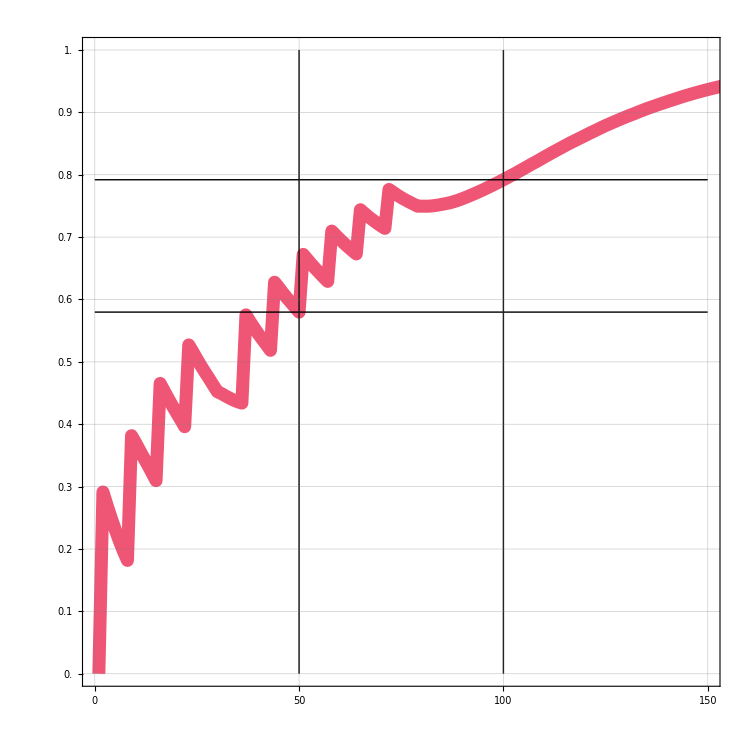

test.pdf

```mathematica
rawData=Import[files[[1]]];
(*--------------------------------------------*)
ratios=1-rawData[[RELSTART;;All]][[All,4]];
a={ratios[[50]],ratios[[100]]}
ListLinePlot[ratios
,AspectRatio->1
,Frame->True
,FrameStyle->Directive[{Opacity[1],hexToRGB["#141759"],Thickness[.015]}]
,FrameTicks->{{Range[0,1,.1],None},{Range[0,365,50],None}}
,FrameTicksStyle->Directive[{20}]
,GridLines->{Range[0,365,50],Range[0,1,.1]}
,ImageSize->750
,InterpolationOrder->1
,PlotRange->{{0,150},{0,1}}
,PlotStyle->{Directive[{Thickness[.0125],Opacity[.9],COLS[[1]]}]}
,Epilog->{
Line[{{50,0},{50,1}}],
Line[{{100,0},{100,1}}],
Line[{{0,a[[1]]},{150,a[[1]]}}],
Line[{{0,a[[2]]},{150,a[[2]]}}]
}
]
Export["test.pdf",%]
```

## Plots

```mathematica
RELSTART=20;
(*--------------------------------------------*)
If[
SEL,
ID="YorkeysKnob";
PATH ="/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/";
confidence=Import["/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/CI.csv"][[2;;All]][[All,3;;All]];
dataRaw={
{{04,01,2011},0.00},{{19,01,2011},0.24},{{01,02,2011},0.70},{{09,02,2011},0.62},{{16,02,2011},0.38},
{{02,03,2011},0.88},{{16,03,2011},0.76},{{30,03,2011},0.98},{{13,04,2011},1.00},{{27,04,2011},0.95}
};
,
ID="Gordonvale";
PATH="/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/GV/Wolbachia_2_10/ANALYZED/";
confidence=Import["/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/GV/CI.csv"][[2;;All]][[All,3;;All]];
dataRaw={
{{04,01,2011},0.00},{{24,01,2011},0.17},{{07,02,2011},0.44},{{21,02,2011},0.49},{{07,03,2011},0.66},
{{21,03,2011},0.68},{{04,04,2011},.79},{{18,04,2011},0.90},{{02,05,2011},.81}
};
];
confidenceZeroed=Prepend[confidence,{0,0}];
dataDates={DateObject[Reverse[#[[1]]]],#[[2]]}&/@dataRaw;
firstDate=dataDates[[1,1]];
dataExp={DateDifference[firstDate,#[[1]],"Day"][[1]],#[[2]]}&/@dataDates;
lines=Line[#]&/@Transpose[{
{#,0}&/@dataExp[[All,1]],
{#,1}&/@dataExp[[All,1]]
}];
(*--------------------------------------------*)
files=FileNames["E_*.csv",PATH];
shading=ListLinePlot[{
Transpose[{dataExp[[All,1]],confidenceZeroed[[All,1]]}],
Transpose[{dataExp[[All,1]],confidenceZeroed[[All,2]]}]
}
,AspectRatio->1
,Frame->True
,FrameStyle->Directive[{Opacity[1],hexToRGB["#141759"],Thickness[.015]}]
,FrameTicks->{{Range[0,1.2,.25],None},{Range[0,365,50],None}}
,FrameTicksStyle->Directive[{0.011}]
,GridLines->{Range[0,365,50],Range[0,1,.25]}
,GridLinesStyle->Directive[{hexToRGB["#141759"],Thickness[.001],Opacity[0.1]}]
,ImageSize->750
,InterpolationOrder->1
,PlotRange->{{-1,150},{0,1.0025}}
,Filling->{1->{{2},{Directive[{COLS[[2]],Opacity[.25]}]}}}
,PlotStyle->{Directive[{Thickness[0.0025],Dashing,Opacity[0],COLS[[2]]}]}
(*,Prolog->Flatten[{Directive[{Darker[COLS[[2]],.1],Opacity[.2],Dashing[.005],Thickness[.001]}],lines}]*)
];
points=ListPlot[dataExp
,AspectRatio->1
,Frame->True
,FrameStyle->Directive[{Opacity[1],hexToRGB["#141759"],Thickness[.015]}]
,FrameTicks->{{Range[0,1.2,.25],None},{Range[0,365,50],None}}
,FrameTicksStyle->Directive[{0.011}]
,GridLines->{Range[0,365,50],Range[0,1,.25]}
,GridLinesStyle->Directive[{hexToRGB["#141759"],Thickness[.001],Opacity[0.1]}]
,ImageSize->750
,InterpolationOrder->1
,PlotMarkers->{Graphics[{Opacity[1],Rectangle[{-.01,-1},{.01,1}],Rectangle[{-1,-.01},{1,.01}]}],Scaled[0.02]}
,PlotRange->{{-1,150},{1,1.0025}}
,PlotStyle->{Directive[{Thickness[.005],PointSize[.01],Opacity[.75],Darker[COLS[[2]],.1]}]}
];
(*Main loop*)
i=10;
Table[
rawData=Import[files[[i]]];
(*--------------------------------------------*)
ratios=1-rawData[[RELSTART;;All]][[All,4]];
plot=ListLinePlot[ratios
,AspectRatio->1
,Frame->True
,FrameStyle->Directive[{Opacity[1],hexToRGB["#141759"],Thickness[.015]}]
,FrameTicks->{{Range[0,1.2,.25],None},{Range[0,365,50],None}}
,FrameTicksStyle->Directive[{0.011}]
,GridLines->{Range[0,365,50],Range[0,1,.25]}
,ImageSize->750
,InterpolationOrder->1
,PlotRange->{{-1,150},{0,1.125}}
,PlotStyle->{Directive[{Thickness[.0125],Opacity[.9],COLS[[1]]}]}
];
overlay=Show[{shading,points, plot}];
Export[PATH<>StringSplit[files[[i]],{"/","."}][[-2]]<>".pdf",overlay,ImageSize->750];
Print[PATH<>StringSplit[files[[i]],{"/","."}][[-2]]<>".pdf"]
(*Export[PATH<>StringSplit[files[[i]],{"/","."}][[-2]]<>".png",overlay,ImageSize->750];*)
,{i,1,Length[files]}];
```

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0001_0000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0001_0050.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0001_0100.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0001_0150.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0001_0200.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0001_0250.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0001_0300.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0001_0350.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0001_0400.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0001_0450.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0001_0500.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0001_0550.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0001_0600.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0001_0650.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0001_0700.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0001_0750.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0001_0800.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0001_0850.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0001_0900.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0001_0950.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0001_1000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0002_0000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0002_0050.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0002_0100.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0002_0150.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0002_0200.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0002_0250.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0002_0300.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0002_0350.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0002_0400.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0002_0450.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0002_0500.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0002_0550.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0002_0600.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0002_0650.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0002_0700.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0002_0750.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0002_0800.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0002_0850.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0002_0900.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0002_0950.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0002_1000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0003_0000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0003_0050.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0003_0100.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0003_0150.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0003_0200.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0003_0250.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0003_0300.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0003_0350.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0003_0400.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0003_0450.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0003_0500.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0003_0550.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0003_0600.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0003_0650.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0003_0700.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0003_0750.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0003_0800.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0003_0850.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0003_0900.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0003_0950.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0003_1000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0004_0000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0004_0050.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0004_0100.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0004_0150.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0004_0200.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0004_0250.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0004_0300.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0004_0350.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0004_0400.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0004_0450.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0004_0500.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0004_0550.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0004_0600.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0004_0650.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0004_0700.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0004_0750.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0004_0800.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0004_0850.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0004_0900.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0004_0950.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0004_1000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0005_0000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0005_0050.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0005_0100.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0005_0150.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0005_0200.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0005_0250.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0005_0300.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0005_0350.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0005_0400.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0005_0450.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0005_0500.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0005_0550.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0005_0600.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0005_0650.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0005_0700.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0005_0750.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0005_0800.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0005_0850.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0005_0900.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0005_0950.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0005_1000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0006_0000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0006_0050.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0006_0100.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0006_0150.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0006_0200.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0006_0250.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0006_0300.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0006_0350.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0006_0400.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0006_0450.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0006_0500.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0006_0550.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0006_0600.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0006_0650.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0006_0700.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0006_0750.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0006_0800.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0006_0850.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0006_0900.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0006_0950.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0006_1000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0007_0000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0007_0050.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0007_0100.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0007_0150.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0007_0200.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0007_0250.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0007_0300.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0007_0350.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0007_0400.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0007_0450.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0007_0500.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0007_0550.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0007_0600.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0007_0650.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0007_0700.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0007_0750.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0007_0800.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0007_0850.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0007_0900.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0007_0950.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0007_1000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0008_0000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0008_0050.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0008_0100.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0008_0150.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0008_0200.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0008_0250.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0008_0300.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0008_0350.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0008_0400.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0008_0450.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0008_0500.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0008_0550.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0008_0600.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0008_0650.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0008_0700.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0008_0750.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0008_0800.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0008_0850.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0008_0900.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0008_0950.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0008_1000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0009_0000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0009_0050.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0009_0100.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0009_0150.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0009_0200.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0009_0250.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0009_0300.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0009_0350.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0009_0400.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0009_0450.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0009_0500.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0009_0550.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0009_0600.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0009_0650.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0009_0700.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0009_0750.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0009_0800.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0009_0850.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0009_0900.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0009_0950.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0009_1000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0010_0000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0010_0050.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0010_0100.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0010_0150.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0010_0200.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0010_0250.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0010_0300.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0010_0350.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0010_0400.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0010_0450.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0010_0500.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0010_0550.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0010_0600.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0010_0650.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0010_0700.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0010_0750.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0010_0800.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0010_0850.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0010_0900.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0010_0950.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0010_1000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0011_0000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0011_0050.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0011_0100.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0011_0150.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0011_0200.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0011_0250.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0011_0300.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0011_0350.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0011_0400.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0011_0450.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0011_0500.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0011_0550.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0011_0600.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0011_0650.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0011_0700.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0011_0750.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0011_0800.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0011_0850.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0011_0900.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0011_0950.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0011_1000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0012_0000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0012_0050.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0012_0100.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0012_0150.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0012_0200.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0012_0250.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0012_0300.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0012_0350.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0012_0400.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0012_0450.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0012_0500.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0012_0550.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0012_0600.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0012_0650.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0012_0700.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0012_0750.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0012_0800.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0012_0850.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0012_0900.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0012_0950.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0012_1000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0013_0000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0013_0050.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0013_0100.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0013_0150.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0013_0200.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0013_0250.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0013_0300.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0013_0350.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0013_0400.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0013_0450.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0013_0500.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0013_0550.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0013_0600.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0013_0650.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0013_0700.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0013_0750.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0013_0800.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0013_0850.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0013_0900.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0013_0950.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0013_1000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0014_0000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0014_0050.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0014_0100.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0014_0150.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0014_0200.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0014_0250.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0014_0300.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0014_0350.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0014_0400.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0014_0450.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0014_0500.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0014_0550.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0014_0600.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0014_0650.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0014_0700.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0014_0750.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0014_0800.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0014_0850.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0014_0900.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0014_0950.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0014_1000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0015_0000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0015_0050.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0015_0100.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0015_0150.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0015_0200.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0015_0250.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0015_0300.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0015_0350.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0015_0400.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0015_0450.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0015_0500.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0015_0550.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0015_0600.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0015_0650.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0015_0700.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0015_0750.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0015_0800.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0015_0850.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0015_0900.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0015_0950.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0015_1000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0016_0000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0016_0050.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0016_0100.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0016_0150.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0016_0200.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0016_0250.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0016_0300.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0016_0350.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0016_0400.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0016_0450.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0016_0500.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0016_0550.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0016_0600.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0016_0650.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0016_0700.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0016_0750.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0016_0800.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0016_0850.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0016_0900.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0016_0950.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0016_1000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0017_0000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0017_0050.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0017_0100.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0017_0150.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0017_0200.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0017_0250.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0017_0300.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0017_0350.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0017_0400.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0017_0450.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0017_0500.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0017_0550.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0017_0600.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0017_0650.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0017_0700.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0017_0750.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0017_0800.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0017_0850.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0017_0900.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0017_0950.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0017_1000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0018_0000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0018_0050.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0018_0100.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0018_0150.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0018_0200.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0018_0250.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0018_0300.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0018_0350.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0018_0400.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0018_0450.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0018_0500.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0018_0550.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0018_0600.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0018_0650.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0018_0700.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0018_0750.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0018_0800.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0018_0850.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0018_0900.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0018_0950.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0018_1000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0019_0000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0019_0050.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0019_0100.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0019_0150.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0019_0200.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0019_0250.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0019_0300.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0019_0350.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0019_0400.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0019_0450.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0019_0500.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0019_0550.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0019_0600.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0019_0650.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0019_0700.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0019_0750.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0019_0800.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0019_0850.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0019_0900.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0019_0950.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0019_1000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0020_0000.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0020_0050.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0020_0100.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0020_0150.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0020_0200.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0020_0250.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0020_0300.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0020_0350.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0020_0400.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0020_0450.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0020_0500.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0020_0550.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0020_0600.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0020_0650.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0020_0700.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0020_0750.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0020_0800.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0020_0850.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0020_0900.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0020_0950.pdf

/Volumes/marshallShare/ThresholdResub/factorialSweep/Fits/YK/Wolbachia_2_10/ANALYZED/E_02_05_0020_1000.pdf